```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3+Subscript[c, 0,4] x^4, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3+Subscript[c, 1,4](x-1)^4, 1<x≤2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3+Subscript[c, 2,4](x-2)^4, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 0,4],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 1,4],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3],Subscript[c, 2,4]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)

c_(1,1)+c_(1,2)+c_(1,3)+c_(1,4)

c_(2,1)+c_(2,2)+c_(2,3)+c_(2,4)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-2)^3 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-2)^3 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)+c_(1,1)+c_(1,2)+c_(1,3)+c_(1,4)+c_(2,1)+c_(2,2)+c_(2,3)+c_(2,4),-2 c_(0,2)-3 c_(0,3)-4 c_(0,4)-2 c_(1,2)-3 c_(1,3)-4 c_(1,4)-2 c_(2,2)-3 c_(2,3)-4 c_(2,4),2 c_(0,2)+3 c_(0,3)+6 c_(0,4)+2 c_(1,2)+3 c_(1,3)+4 c_(1,4)+2 c_(2,2)+3 c_(2,3)+4 c_(2,4)+2 (c_(1,4)+c_(2,4)),-4 c_(0,4)-4 (c_(1,4)+c_(2,4)),2 c_(0,4)+2 (c_(1,4)+c_(2,4))}

{1+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)+2 c_(1,1)+2 c_(1,2)+2 c_(1,3)+2 c_(1,4)+3 c_(2,1)+3 c_(2,2)+3 c_(2,3)+3 c_(2,4),-c_(0,1)-2 c_(0,2)-3 c_(0,3)-4 c_(0,4)-3 c_(1,1)-4 c_(1,2)-6 c_(1,3)-8 c_(1,4)-5 c_(2,1)-6 c_(2,2)-9 c_(2,3)-12 c_(2,4),c_(0,2)+3 c_(0,3)+6 c_(0,4)+c_(1,2)+6 c_(1,3)+12 c_(1,4)+c_(2,2)+9 c_(2,3)+18 c_(2,4),-c_(0,3)-4 c_(0,4)-3 c_(1,3)-8 c_(1,4)-5 c_(2,3)-12 c_(2,4),c_(0,4)+c_(1,4)+c_(2,4)}

```mathematica
(*Smoothness*)
Dh=Simplify[D[h[x],x],x>0];
S0=(Dh/.x->0)==0
S1=Limit[Dh,x->1,Direction->1]==Limit[Dh,x->1,Direction->-1]
S2=Limit[Dh,x->2,Direction->1]==Limit[Dh,x->2,Direction->-1]
S3=Limit[Dh,x->3,Direction->1]==Limit[Dh,x->3,Direction->-1]
```

c_(0,1)==0

c_(0,1)+2 c_(0,2)+3 c_(0,3)+4 c_(0,4)==c_(1,1)

c_(1,1)+2 c_(1,2)+3 c_(1,3)+4 c_(1,4)==c_(2,1)

c_(2,1)+2 c_(2,2)+3 c_(2,3)+4 c_(2,4)==0

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0,
	S0,S1,S2,S3
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,1)→0,c_(0,4)→-1-c_(0,2)-c_(0,3),c_(1,1)→-4-2 c_(0,2)-c_(0,3),c_(1,3)→41/4+5 c_(0,2)+(5 c_(0,3))/2-2 c_(1,2),c_(1,4)→-25/4-3 c_(0,2)-(3 c_(0,3))/2+c_(1,2),c_(2,1)→7/4+c_(0,2)+(c_(0,3))/2,c_(2,2)→15/4+2 c_(0,2)+(3 c_(0,3))/2-c_(1,2),c_(2,3)→-51/4-7 c_(0,2)-(9 c_(0,3))/2+2 c_(1,2),c_(2,4)→29/4+4 c_(0,2)+(5 c_(0,3))/2-c_(1,2)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]
```

{{-2,3},{-2,2},{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2},{3,-2},{3,-3}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

1/541900800(710720512 c_(0,2)^4+64 c_(0,2)^3 (96603491+22528790 c_(0,3)-4600728 c_(1,2))+16 c_(0,2)^2 (1265098369+68874844 c_(0,3)^2+c_(0,3) (581444444-28506576 c_(1,2))-114586848 c_(1,2)+3206976 c_(1,2)^2)+12 c_(0,2) (2419537509+31366520 c_(0,3)^3-324109624 c_(1,2)+16680064 c_(1,2)^2-362496 c_(1,2)^3-4 c_(0,3)^2 (-97444621+4942360 c_(1,2))+2 c_(0,3) (843003883-77532480 c_(1,2)+2257792 c_(1,2)^2))+3 (5110913111+16186224 c_(0,3)^4-916196400 c_(1,2)+71761216 c_(1,2)^2-2433024 c_(1,2)^3+53248 c_(1,2)^4-32 c_(0,3)^3 (-8176477+433050 c_(1,2))+8 c_(0,3)^2 (211536105-19640784 c_(1,2)+606304 c_(1,2)^2)-8 c_(0,3) (-604723137+82614294 c_(1,2)-4205536 c_(1,2)^2+100352 c_(1,2)^3)))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.0497664 | True

{c_(0,1)→0,c_(0,4)→0.309775,c_(1,1)→-0.838311,c_(1,3)→0.958101,c_(1,4)→-0.813628,c_(2,1)→0.169156,c_(2,2)→0.165542,c_(2,3)→-0.83855,c_(2,4)→0.503853,c_(0,2)→-1.85191,c_(0,3)→0.542138,c_(1,2)→0.693839}

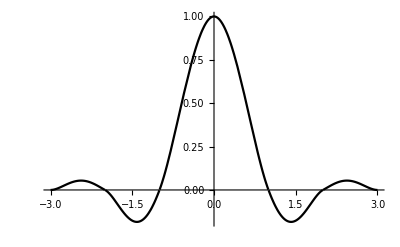

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```